Autor: Artur Bednarczyk

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 1

Metody Rungego-Kutty

Napisać procedury realizujące algorytmy metod Rungego-Kutty rzędu trzeciego i rzędu czwartego (argumenty:  f, x_0, y_0, h, n).

Korzystając z napisanych procedur wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=(x y(x) - y^2(x))/x^2,
y(1)=2.

Obliczenia wykonać dla 20 kroków o długości 0.1.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.

## Rozwiązanie

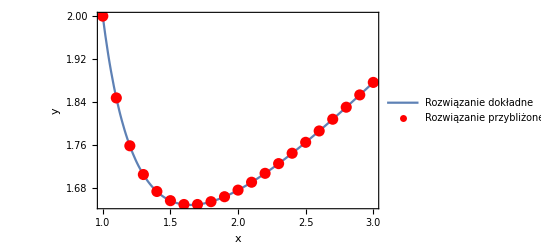

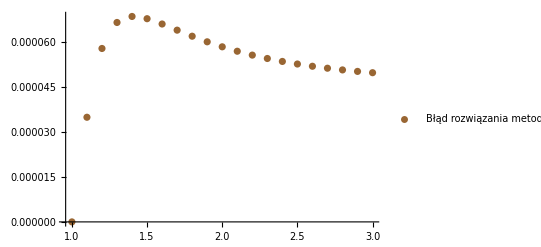

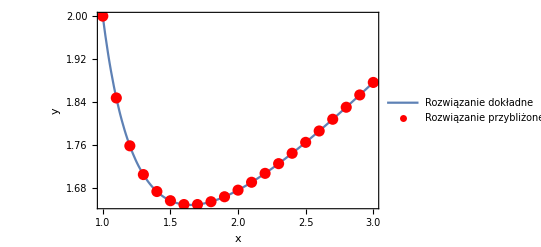

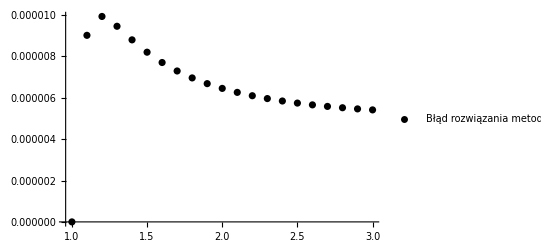

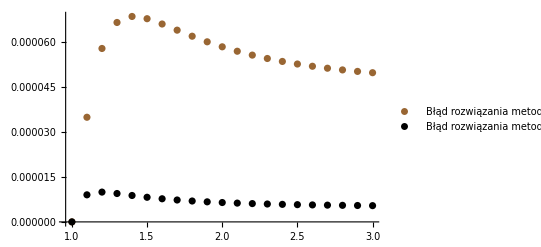

```mathematica
(* Badana Funkcja *)
func[x_, y_]:=(x*y-y^2)/x^2;
(* Metoda Rungego-Kutty rzędu trzeciego *)
mrk3[f_,x0_,y0_,h_,n_]:=Module[{x,y,results},
x = x0;
y = y0;
results = {{x,y}};
Do[
k1 = f[x,y];
k2 =f[x+1/2 h, y +1/2 h*k1];
k3 = f[x+h,y-h*k1+2h*k2];
x = x + h;
y = y + 1/6 h*(k1 + 4k2 + k3);
AppendTo[results, {x,y}];
,{i,1, n}];

Return [results];
];
(* Metoda Rungego-Kutty rzędu czwartego *)
mrk4[f_,x0_,y0_,h_,n_]:=Module[{x,y,results},
x = x0;
y = y0;
results = {{x,y}};
Do[
k1 = f[x,y];
k2 =f[x+1/2 h, y +1/2 h*k1];
k3 = f[x+1/2 h,y+1/2 h*k2];
k4 = f[x+h, y+h*k3];
x = x + h;
y = y + 1/6 h*(k1 + 2k2 + 2k3 + k4);
AppendTo[results, {x,y}];
,{i,1, n}];

Return [results];
];
(* Rozwiązanie dokładne *)
result = DSolve[{yy'[x]==(x*yy[x]-(yy[x])^2)/x^2, yy[1]==2}, yy[x],x];
res = result⟦1,1,2⟧;
resPoints = Table[res/.{x->i}, {i, 1,3,.1}];
resultPlot = Plot[res, {x,1,3}, PlotLegends->LineLegend[{"Rozwiązanie dokładne"}]];
(* Rozwiązanie i wykres dla metody rzędu trzeciego *)
mrk3res = mrk3[func,1,2,.1,20];
mrk3Plot = ListPlot[mrk3res,PlotStyle->{PointSize[.02],Red}, PlotLegends->LineLegend[{"Rozwiązanie przybliżone"}]];
Show[resultPlot, mrk3Plot, {Frame->True, FrameLabel->{"x","y", "Metoda Rungego-Kutty rzędu trzeciego"}}]
(* Błędy *)
error3 = Table[{mrk3res⟦i,1⟧, Abs[mrk3res⟦i,2⟧-resPoints⟦i⟧]}, {i,1,21}];
error3Plot = ListPlot[error3, PlotStyle->{Brown},PlotLegends->LineLegend[{"Błąd rozwiązania metodą rzędu trzeciego"}]];
Show[error3Plot]
(* Rozwiązanie i wykres dla metody rzędu czwartego *)
mrk4res = mrk4[func, 1, 2,.1,20];
mrk4Plot = ListPlot[mrk4res,PlotStyle->{PointSize[.02],Red}, PlotLegends->LineLegend[{"Rozwiązanie przybliżone"}]];
Show[resultPlot, mrk4Plot, {Frame->True, FrameLabel->{"x","y", "Metoda Rungego-Kutty rzędu czwartego"}}]
(* Błędy *)
error4 = Table[{mrk4res⟦i,1⟧, Abs[mrk4res⟦i,2⟧-resPoints⟦i⟧]}, {i,1,21}];
error4Plot = ListPlot[error4,PlotStyle->{Black}, PlotLegends->LineLegend[{"Błąd rozwiązania metodą rzędu czwartego"}]];
Show[error4Plot]
(*  *)
Show[error3Plot, error4Plot]
```